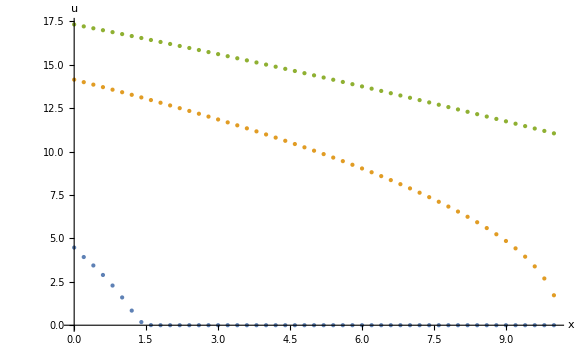

```mathematica
ClearAll["Global`*"];(*Plot[{Subscript[N,0],value[[1]]/.plots,value[[2]]/.plots,value[[3]]/.plots},{t,0,T},PlotStyle->{{Green,Dashed},Orange,Red,Gray},PlotLegends->Placed[{"Subscript[N, 0]","X(t)","Y(t)","Z(t)"},Above],AxesLabel->{"t","X,Y,Z"}] PlotRange->All,ImageSize->Medium*)data1=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 2\\program\\Проект1\\Проект1\\SOLVE1.txt","Data"];data2=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 2\\program\\Проект1\\Проект1\\SOLVE2.txt","Data"];data3=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 2\\program\\Проект1\\Проект1\\SOLVE3.txt","Data"];
(*data4=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 2\\program\\Проект1\\Проект1\\SOLVE4.txt","Data"];data5=Import["C:\\Users\\тимофей\\Desktop\\BMSTU\\6 семестр\\Методы вычислений\\лабы\\лаба 2\\program\\Проект1\\Проект1\\SOLVE5.txt","Data"];*)

ListPlot[{data1,data2,data3(*,data4,data5*)},AxesLabel->{"x","u"},AxesStyle->Thick,LabelStyle->Directive[20],(*PlotLegends->{"t=0","t=0.006","t=0.012","t=0.078","t=0.12"},*)PlotStyle->PointSize[Medium],PlotRange->All]
```

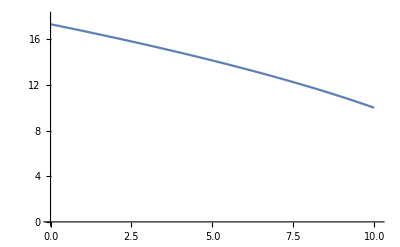

```mathematica
k=15000;
Plot[20^0.5(5*0.0002*k-x)^0.5,{x,0,10},PlotRange->{{0,10.1},{0,18}}]
```